## Set inputs

#### IDM

```mathematica
ClearAll["Global`*"]
lambdaHfrommasses[mH_,mu2_]:=(2(mH^2-mu2^2))/v^2
lambdaAfrommasses[mA_,mu2_]:=(2(mA^2-mu2^2))/v^2
lambda3frommasses[mHp_,mu2_]:=(2(mHp^2-mu2^2))/v^2
lambda4frommasses[mH_,mA_,mHp_,mu2_]:=1/2(lambdaHfrommasses[mH,mu2]+lambdaAfrommasses[mA,mu2])-lambda3frommasses[mHp,mu2]
lambda5frommasses[mH_,mA_,mu2_]:=1/2(lambdaHfrommasses[mH,mu2]-lambdaAfrommasses[mA,mu2])
lambdaHfromlambdas[l3_,l4_,l5_]:=l3+l4+l5
lambdaAfromlambdas[l3_,l4_,l5_]:=l3+l4-l5
```

#### Z2SSM

```mathematica
lambdaHSfrommasses[mS_,muS_]:=(2(mS^2-muS^2))/v^2
```

## Top quark mass

```mathematica
mt2[h_]:=Mt^2(1+h/v)^2
```

## IDM

```mathematica
Clear[l1,l2,l3,l4,l5,v,mu2]
```

```mathematica
(* Higgs-field dependence only *)
mH2$h[h_]:=mu2^2+1/2 lamH (v+h)^2
mA2$h[h_]:=mu2^2+1/2 lamA(v+h)^2
mHp2$h[h_]:=mu2^2+1/2 lam3 (v+h)^2
```

```mathematica
(* full field dependence*)
fieldrep$IDM={Phi1|Phi1c->{0,1/(√2)(v+h)},Phi2->{Hp,1/(√2)(H+ⅈ A)},Phi2c->{Hm,1/(√2)(H-ⅈ A)}};(* unitary gauge *)
Vtree$IDM=mu12 Phi1.Phi1c+mu2^2 Phi2.Phi2c+1/2 l1(Phi1.Phi1c)^2+1/2 l2(Phi2.Phi2c)^2+l3 (Phi1.Phi1c)(Phi2.Phi2c)+l4 (Phi1c.Phi2)(Phi1.Phi2c)+1/2l5((Phi1.Phi2c)^2+(Phi1c.Phi2)^2)//.fieldrep$IDM//Expand//Simplify
```

1/8 (h^4 l1+A^4 l2+H^4 l2+4 H^2 Hm Hp l2+4 Hm^2 Hp^2 l2+4 H^2 mu2^2+8 Hm Hp mu2^2+4 h^3 l1 v+2 H^2 l3 v^2+4 Hm Hp l3 v^2+2 H^2 l4 v^2+2 H^2 l5 v^2+4 mu12 v^2+l1 v^4+4 h v (2 Hm Hp l3+A^2 (l3+l4-l5)+H^2 (l3+l4+l5)+2 mu12+l1 v^2)+2 h^2 (2 Hm Hp l3+A^2 (l3+l4-l5)+H^2 (l3+l4+l5)+2 mu12+3 l1 v^2)+2 A^2 (H^2 l2+2 Hm Hp l2+2 mu2^2+l3 v^2+l4 v^2-l5 v^2))

```mathematica
D[Vtree$IDM,{H,2}]/.Hp->0//FullSimplify
D[Vtree$IDM,{A,2}]/.Hp->0//FullSimplify
D[Vtree$IDM,Hp,Hm]/.Hp->0//FullSimplify
```

1/2 (A^2 l2+3 H^2 l2+2 mu2^2+(l3+l4+l5) (h+v)^2)

1/2 (3 A^2 l2+H^2 l2+2 mu2^2+(l3+l4-l5) (h+v)^2)

1/2 ((A^2+H^2) l2+2 mu2^2+l3 (h+v)^2)

```mathematica
mH2[h_,H_,A_]:=mu2^2+1/2(l3+l4+l5)(v+h)^2+3/2 l2 H^2+1/2 l2 A^2
mA2[h_,H_,A_]:=mu2^2+1/2(l3+l4-l5)(v+h)^2+1/2 l2 H^2+3/2 l2 A^2
mHp2[h_,H_,A_]:=mu2^2+1/2 l3(v+h)^2+1/2 l2 (H^2+ A^2)
```

```mathematica
D[Vtree$IDM,{h,1}]/.H|A|Hp|h->0//FullSimplify
D[Vtree$IDM,{h,2}]/.H|A|Hp|h->0//FullSimplify
```

mu12 v+(l1 v^3)/2

mu12+(3 l1 v^2)/2

```mathematica
Veff$IDM$0L[h_,H_,A_]:=1/8 (h^4 l1+A^4 l2+H^4 l2+4 H^2 mu2^2+4 h^3 l1 v+2 H^2 l3 v^2+2 H^2 l4 v^2+2 H^2 l5 v^2+4 mu12 v^2+l1 v^4+4 h v (A^2 (l3+l4-l5)+H^2 (l3+l4+l5)+2 mu12+l1 v^2)+2 h^2 (A^2 (l3+l4-l5)+H^2 (l3+l4+l5)+2 mu12+3 l1 v^2)+2 A^2 (H^2 l2+2 mu2^2+l3 v^2+l4 v^2-l5 v^2))
```

## Z2SSM

```mathematica
Clear[muSM, muS, lam,lamHS,lamS]
```

```mathematica
(* Higgs-field dependence only *)
mS2$h[h_]:=muS^2+1/2 lamHS (v+h)^2
```

```mathematica
(* full field dependence *)
```

```mathematica
fieldrep$Z2SSM={phi-> 1/(√2)(v+h)}; (* unitary gauge *)
Vtree$Z2SSM=muSM phi^2+1/2 muS^2 S^2+1/2 lam phi^4+1/2 lamHS S^2 phi^2+1/2 lamS S^4/.fieldrep$Z2SSM
tadrep$Z2SSM=Solve[(D[Vtree$Z2SSM,h]/.h->0)==0,muSM][[1]];
D[Vtree$Z2SSM,{S,2}]
mS2[h_,S_]:=muS^2+6 lamS S^2+1/2 lamHS (h+v)^2
```

(muS^2 S^2)/2+(lamS S^4)/2+1/2 muSM (h+v)^2+1/4 lamHS S^2 (h+v)^2+1/8 lam (h+v)^4

muS^2+6 lamS S^2+1/2 lamHS (h+v)^2

```mathematica
Veff$Z2SSM$0L[h_,S_]:=(muS^2 S^2)/2+(lamS S^4)/2+1/2 muSM (h+v)^2+1/4 lamHS S^2 (h+v)^2+1/8 lam (h+v)^4
```

## 1L effective potential

```mathematica
f[x_]:=x^2/4(Log[x/Qren^2]-3/2)
```

```mathematica
(* below: 1-loop results for the effective potential in the IDM and Z2SSM **ONLY WITH TOP QUARK AND BSM SCALARS** *)
```

```mathematica
Veff$IDM$1L[h_,H_,A_]:=1/(16 π^2)(-12 f[mt2[h]]+f[mH2[h,H,A]]+f[mA2[h,H,A]]+2f[mHp2[h,H,A]])
(* factor -12 for top quark comes from (-1) from fermion loop times 3 from number of colours times 4 from number of d.o.f in a Dirac fermion;
factor 2 for charged Higgs boson loop comes number of d.o.f for a charged scalar *)
Veff$Z2SSM$1L[h_,S_]:=1/(16 π^2)(-12 f[mt2[h]]+f[mS2[h,S]])
```

```mathematica
(* total (i.e. tree-level+1L) effective potential *)
Veff$IDM[h_,H_,A_]:=Veff$IDM$0L[h,H,A]+Veff$IDM$1L[h,H,A]
Veff$Z2SSM[h_,S_]:=Veff$Z2SSM$0L[h,S]+Veff$Z2SSM$1L[h,S]
```

## Numerical examples

### IDM

```mathematica
mHi=500;mAi=525;mHpi=525;mu2=400;Qren=172.5;l2=2;
Mt=172.5;
v=246.22;
Mh=125.09;
l1=Mh^2/v^2;
mu12=-l1 v^2/2;
l4=lambda4frommasses[mHi,mAi,mHpi,mu2];
l5=lambda5frommasses[mHi,mAi,mu2];
l3=lambda3frommasses[mHpi,mu2];
```

```mathematica
Veff$IDM$1L[0,0,0]
```

3.49361×10^8

```mathematica
Veff$IDM[v,0,0]
```

4.39732×10^9

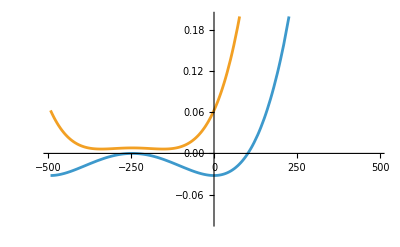

```mathematica
Plot[{Veff$IDM$0L[h,0,0]/v^4,Veff$IDM[h,0,0]/v^4},{h,-2v,2v},PlotRange->{-0.1,0.2}]
```

### Z2SSM

```mathematica
mSi=500;muS=400;Qren=172.5;lamS=2;
Mt=172.5;
v=246.22;
Mh=125.09;
lam=Mh^2/v^2;
muSM=-lam v^2/2;
lamHS=lambdaHSfrommasses[mSi,muS];
```

```mathematica
Veff$Z2SSM[v,0]/v^4
```

2.72086×10^-10 Veff$Z2SSM[246.22,0]

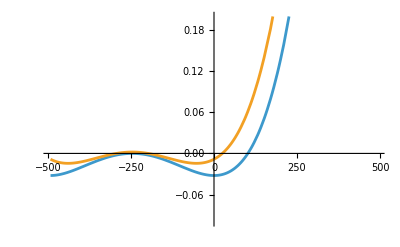

```mathematica
Plot[{Veff$Z2SSM$0L[h,0]/v^4,Veff$Z2SSM[h,0]/v^4},{h,-2v,2v},PlotRange->{-0.1,0.2}]
```

## New plots

```mathematica
Plot3D[{Veff$Z2SSM[h,S]/v^4}, {h,-2.2v,0.2v},{S, -v/4, v/4},AxesLabel->{h, S, "V_(1  L)(h, S)"},  LabelStyle->{FontSize->14}]
```

-Graphics3D-